# ME712 Applied Mathematics in Mechanics

Prof. Douglas P. Holmes
Mechanical Engineering
Boston University

## Regular Perturbation: Introduction

Here’s a simple, second order polynomial:

```mathematica
f[x_,ϵ_]:=x^2+2ϵ x -1
```

Feel free to change the polynomial here. If you enter a higher order polynomial, we may need to adjust some of the commands used in substituting solutions at each order of ϵ below.

### Analytical Solution

The function f[x,ϵ] is a second order polynomial, so it can be solved analytically using Solve[ ]. The term “x /.” means replace x with the result of Solve - delete it to see the difference.

```mathematica
sol=x/.Solve[f[x,ϵ]==0,x]
```

{-ϵ-√(1+ϵ^2),-ϵ+√(1+ϵ^2)}

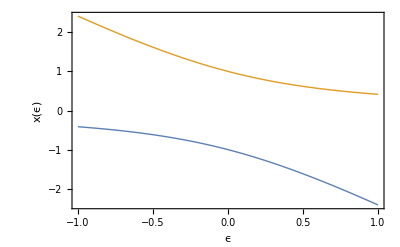

```mathematica
aPlot=Plot[sol, {ϵ,-1, 1}, Frame-> True, FrameLabel->{"ϵ","x(ϵ)"}, PlotStyle->Thick]
```

### Approximate Solution: Power Series Expansion

It would be more appropriate to introduce a series expansion without assuming we can use integer powers of ϵ. However, for the sake of introducing both the regular perturbation and some of the less intuitive parts of Mathematica, let’s start with a simple Taylor series expansion.

Notes on the line below:
(1) := means “Set Delayed”.  Mathematica won’t evaluate this function until we call it later. That is useful here since we haven’t specified “n”, i.e. the order to take the expansion to.
(2) Normal[ ] removes the + O(ϵ^(n+1)) from the output of expansion[n]. Mathematica has trouble doing calculations when those terms are present.

```mathematica
expansion[n_]:=Normal[Series[x[ϵ], {ϵ,0,n}]]
```

For example, let’s look at a second order Taylor series expansion:

```mathematica
expansion[2]
```

x[0]+ϵ x'[0]+1/2 ϵ^2 x''[0]

### Approximate Solution: O(1)

Let’s start with a zeroth order approximation in ϵ

```mathematica
expansion[0]
```

x[0]

We insert the first order approximation for x ~ x[0] into f[x,ϵ] with ϵ=0. Then, solve f[x,ϵ] for x[0].

```mathematica
solX0=x[0]/.Solve[f[expansion[0],0]==0,x[0]]
```

{-1,1}

Finally, insert our solutions for x[0] back into our first order expansion for x. This, of course, seems silly since the first order expansion of x is x~x[0], but let’s just do it for completeness.

```mathematica
ord1=expansion[0]/.x[0]->solX0
```

{-1,1}

```mathematica
ord1Plot=Plot[ord1,{ϵ,-1,1}, PlotStyle->Dotted];
```

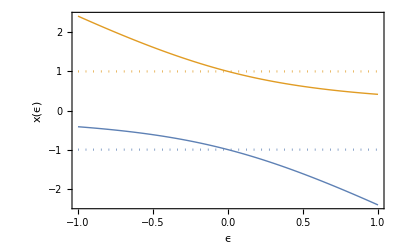

```mathematica
Show[aPlot,ord1Plot]
```

The first order approximation captures x(ϵ) around ϵ ~ 0.

### Approximate Solution: O(ϵ)

Let’s look at the first order approximation in ϵ

```mathematica
expansion[1]
```

x[0]+ϵ x'[0]

Next, insert this expansion into f[x,ϵ], replace x[0] with our first order solution.

```mathematica
exEp=f[expansion[1],ϵ]/.x[0]-> ord1
```

{-1+2 ϵ (-1+ϵ x'[0])+(-1+ϵ x'[0])^2,-1+2 ϵ (1+ϵ x'[0])+(1+ϵ x'[0])^2}

Before we can solve for the order ϵ  term, we have to get rid of the higher order terms in the equation above. The easiest way to do that is by Taylor expanding exEp to first order (and use Normal[ ] to clean it up). Then we solve. Here, its all done in the same line.

```mathematica
solX01a=x'[0]/.Solve[Normal[Series[exEp,{ϵ,0,1}]][[1]]==0,x'[0]][[1]];
solX01b=x'[0]/.Solve[Normal[Series[exEp,{ϵ,0,1}]][[2]]==0,x'[0]][[1]];
```

There are two solutions for x’[0]:

```mathematica
solX01={solX01a,solX01b}
```

{-1,-1}

```mathematica
ordEpa=expansion[1]/.x[0]->solX0[[1]]/.x'[0]-> solX01a;
ordEpb=expansion[1]/.x[0]->solX0[[2]]/.x'[0]-> solX01b;
```

```mathematica
ordEp={ordEpa,ordEpb}
```

{-1-ϵ,1-ϵ}

```mathematica
ordEpPlot=Plot[ordEp,{ϵ,-1,1}, PlotStyle->Dashed];
```

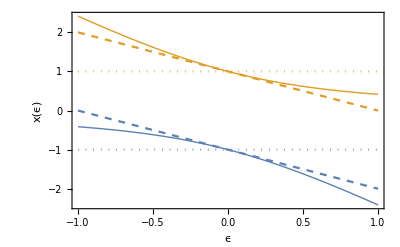

```mathematica
Show[aPlot,ord1Plot, ordEpPlot]
```

The order ϵ solution looks pretty good out to ϵ ~ 0.25

### Approximate Solution: O(ϵ^2)

Now we look at the second order in ϵ

```mathematica
expansion[2]
```

x[0]+ϵ x'[0]+1/2 ϵ^2 x''[0]

```mathematica
exEp2=f[expansion[2],ϵ]/.x[0]-> solX0
```

{-1+2 ϵ (-1+ϵ x'[0]+1/2 ϵ^2 x''[0])+(-1+ϵ x'[0]+1/2 ϵ^2 x''[0])^2,-1+2 ϵ (1+ϵ x'[0]+1/2 ϵ^2 x''[0])+(1+ϵ x'[0]+1/2 ϵ^2 x''[0])^2}

```mathematica
truncEp2=Normal[Series[f[expansion[2],ϵ] ,{ϵ,0,2}]]/.x[0]-> ord1
```

{2 ϵ (-1-x'[0])+ϵ^2 (2 x'[0]+x'[0]^2-x''[0]),2 ϵ (1+x'[0])+ϵ^2 (2 x'[0]+x'[0]^2+x''[0])}

```mathematica
solX011a =x''[0]/.Solve[truncEp2[[1]]==0/.x'[0]-> solX01a, x''[0]][[1]];
solX011b =x''[0]/.Solve[truncEp2[[2]]==0/.x'[0]-> solX01b, x''[0]][[1]];
```

```mathematica
solX011={solX011a,solX011b}
```

{-1,1}

```mathematica
ordEp2a=expansion[2]/.x[0]->solX0[[1]]/.x'[0]-> solX01a/.x''[0]-> solX011a;
ordEp2b=expansion[2]/.x[0]->solX0[[2]]/.x'[0]-> solX01b/.x''[0]-> solX011b;
```

```mathematica
ordEp2={ordEp2a,ordEp2b}
```

{-1-ϵ-ϵ^2/2,1-ϵ+ϵ^2/2}

```mathematica
ordEp2Plot=Plot[ordEp2,{ϵ,-1,1}, PlotStyle->DotDashed];
```

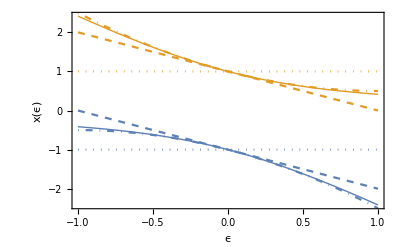

```mathematica
Show[aPlot,ord1Plot, ordEpPlot, ordEp2Plot]
```

The second order expansion in ϵ  works quite well out to ϵ~1.

### Asymptotic Expansion

Finally, we can look at the the formal definition of the asymptotic expansion by checking that the following limits hold at each order of the expansion:

```mathematica
Limit[sol-ord1,ϵ->0]
```

{0,0}

```mathematica
Limit[(sol-ordEp)/ϵ,ϵ->0]
```

{0,0}

```mathematica
Limit[(sol-ordEp2)/ϵ^2,ϵ->0]
```

{0,0}

## Showing Off with Mathematica

#### Just to show off the power of Mathematica, here is how to solve this problem with one line. Note: I have only solved for one of the two roots. This could be extended for more...

```mathematica
nnExpansion[ϵ_,nnn_]:=1+(ϵ^Range[1,nnn]).Solve[Thread[CoefficientList[Normal[Series[f[1+Sum[a[n] ϵ^n,{n,1,nnn}],ϵ], {ϵ,0,nnn}]], ϵ] == Normal[SparseArray[{}, {nnn + 1, 1}]]], Table[a[n], {n,1,nnn}]][[1]][[All,2]]
```

#### Let’s go out to 10th order

```mathematica
nnExpansion[ϵ,10]
```

1-ϵ+ϵ^2/2-ϵ^4/8+ϵ^6/16-(5 ϵ^8)/128+(7 ϵ^10)/256

#### ...and here is how to generate the approximation changes at each order”

```mathematica
Manipulate[
1+(ϵ^Range[1,nnn]).Solve[Thread[CoefficientList[Normal[Series[f[1+Sum[a[n] ϵ^n,{n,1,nnn}],ϵ], {ϵ,0,nnn}]], ϵ] == Normal[SparseArray[{}, {nnn + 1, 1}]]], Table[a[n], {n,1,nnn}]][[1]][[All,2]], {nnn,1,8,1, Appearance->"Labeled"}]
```

#### ...and here is how to visualize how the order of the expansion helps approximate the function as ϵ~1.

```mathematica
Manipulate[Plot[
{Evaluate[nnExpansion[ϵ,nnn]],
{Evaluate[
x/.{ToRules[Roots[f[x,ϵ]==0,x]]}
]
}
},{ϵ,10^-4,1},PlotRange->{{10^-4,10^0},{0,2}}, AxesLabel->{"ϵ","x"}],{nnn,1,12,1, Appearance->"Labeled"}]
```